```mathematica
(*Functions*)

(*TODO: comments*)

(* Given a submodule V{i} returns its vectors in new basis in which the 2^Nx2^N group 
representation of symmetric group Nis blockdiagonalized to irreduceble blocks;*)
BlockBasis[vi_,n_,i_]:=
Module[{y,ortho,v},
v[i]=vi;
(*case i=0, n=i
1D irrep*)
If[i==0 || i==n ,y[i]=v[i]];
(*case i=1, i=n-1*)
If[i==1 || i==n-1,
(*The 1D irrep*)
y[i]={Total[v[i]]};

(*N-1 dimensional irrep*)
(*Find the ortogonal complement and obtain orthogonalized basis vectors for it*)
ortho[i]=Join[NullSpace[v[i]],y[i]];
y[{i,i}]=Orthogonalize[NullSpace[ortho[i]]];
y[i]=Join[y[i],y[{i,i}]];
];

(*case i>1*)
If[i>1 && i<n-1,
(*Slightly different procedure for depending on if i≤N/2*)
If[i≤n/2,
(*Separete the subspace, v{i,i-1}, corresponding to submodule W(0)+..W(i-1)*)
v[{i,i-1}]=SubModule[vi,n,i];  
(*obtain new basis for v{i,i-1}*)
y[{i,i-1}]=BlockBasis[v[{i,i-1}],n,i-1];
(*Find the orthogonal complement of v{i,i-1} and obtain orthogonalized set of basis vectors*)
ortho[{i,i}]=Join[NullSpace[v[i]],v[{i,i-1}]];
y[{i,i}]=Orthogonalize[NullSpace[ortho[{i,i}]]];
y[i]=Join[y[{i,i}],y[{i,i-1}]];
]
If[i>n/2,
v[{i,i+1}]=SubModule[vi,n,i];
y[{i,i+1}]=BlockBasis[v[{i,i+1}],n,i+1];
ortho[{i,i}]=Join[NullSpace[v[i]],v[{i,i+1}]];
y[{i,i}]=Orthogonalize[NullSpace[ortho[{i,i}]]];
y[i]=Join[y[{i,i}],y[{i,i+1}]];
]
];
y[i]]

(*get n-dimensional vector space*)
VectorSpace[n_]:=
Module[{v,i},
v=List[];
For[i=1,i≤2^n,i++,
v=Append[v,Array[If[#==i,1,0]&,2^n]];
];
v]

(*get the subspace of V corresponding to states with with i bits equal to one*)
SubSpaceVi[v_,i_]:=                                                                                                                          (*RENAME TO getSubSpaceVi*)
Module[{vi,j},
vi={};
For[j=1,j≤Length[v],j++,
If[DigitCount[j-1,2,1]==i,vi=Append[vi,v[[j]]]];
];
vi]

(*returns vector basis corresponding to the part of V{i} isomorphic to W{i-1}*)
SubModule[vi_,n_,i_]:=
Module[{vii1,newVi,j,k,k1,k2,xj,subSetsI,set}, 

(*Associate each of the vectors in V{i} with a set of i numbers, which correspond to the 1s in the strings corresponding to each vector*)
(*e.g. N=4, i=2; 1100 -> V{1,2}*)
subSetsI=Sort[Subsets[Range[n],{i}],Binary2Dec[#1]≤Binary2Dec[#2]&]; (* NOTE: always order in binary asecending order to avoid confusion!!!*)
For[k=1,k<=Length[subSetsI],k++,
newVi[subSetsI[[k]]]=vi[[k]];
];


(*Form the vectors x(j) as described in 2)c)i) in the desrciption of the procedure*)
vii1={};
(*Case i<=n/2*)
If[i≤n/2, 
(*Obtain the subsets of length i-1 which correspond to vectors x(j) and biject V{i} w.r.t. to 1 at the j position*)
j=Sort[Subsets[Range[n],{i-1}],Binary2Dec[#1]≤Binary2Dec[#2]&];    (* NOTE: always order in binary asecending order to avoid confusion!!!*)
(*Loop over the subsets to obtain vectors x(j)*)
For[k1=1,k1≤Length[j],k1++,
If[k1>1,vii1=Append[vii1,xj]]; 
xj=Array[0&,2^n];
(*Sum the required vectors of V{i} to obtain x(j)*)
For[k2=1,k2≤n,k2++,
If[!MemberQ[j[[k1]],k2],
set=Sort[Join[j[[k1]],{k2}]];
xj=xj+newVi[set];
];
];
];
vii1=Append[vii1,xj];
];
(*Case i>n/2*)
If[i>n/2,
j=Sort[Subsets[Range[n],{i+1}],Binary2Dec[#1]≤Binary2Dec[#2]&];  
For[k1=1,k1≤Length[j],k1++,
If[k1>1,vii1=Append[vii1,xj]]; 
xj=Array[0&,2^n];
For[k2=1,k2≤n,k2++,
If[MemberQ[j[[k1]],k2],
set=Sort[DeleteCases[j[[k1]],k2]];
xj=xj+newVi[set];
]
]
];
vii1=Append[vii1,xj];
];
vii1]

(*Conver a set of numbers, corresponding to position of 1s in the string, to decimal number
Note: count from 1 not 0
Example: {} ->1, {1}-> 2, {1,2} -> 4, etc *)
Binary2Dec[l_]:=
Module[{num,j},
num=1;
For[j=1,j<=Length[l],j++,
num=num +2^(l[[j]]-1);
];
num]


(*<<<<<<<<<<<<<<<<<<<<<<USER FUNCTIONs>>>>>>>>>>>>>>>>>>>>>>>>*)

(*get 2^Nx2^N matrix representation of the S(n) group element corresponding to pair permuitation (i,j)*)
getSn[n_,i_,j_]:=
Module[{sn,subSets,v},
sn=VectorSpace[n];
subSets=DeleteCases[Range[n],i];
subSets=DeleteCases[subSets,j];
subSets=Subsets[subSets];
For[k=1,k≤Length[subSets],k++,
v=sn[[2^(i-1)+Binary2Dec[subSets[[k]]]]];
sn[[2^(i-1)+Binary2Dec[subSets[[k]]]]]=sn[[2^(j-1)+Binary2Dec[subSets[[k]]]]];
sn[[2^(j-1)+Binary2Dec[subSets[[k]]]]]=v;
];
sn]

(*get a plot of the block form of symmetric group N*)
(*TODO: needs improvement*)
BlockPlot[n_]:=
Module[{sum,i,s},
sum=VectorSpace[n];
For[i=1,i≤n,i++,
sum=sum+getSn[n,i,1];
If[i>2,sum=sum+getSn[n,i,i-1]];
];

s=TransformMatrix[n];
Transpose[s].sum.s //MatrixPlot]


(*get the transformation matrix for Symmetry group N*)
TransformMatrix[n_]:=
Module[{V,Y,y,s,i},
V=VectorSpace[n];
(*Obtain the transformation basis for each subspace V{i}*)
For[i=0,i≤n,i++,
y[i]=BlockBasis[SubSpaceVi[V,i],n,i];
If[i==0,Y=Join[y[i]],Y=Join[Y,y[i]]];
];

(*Normalize the vectors to obtain unitary matrix*)
For[i=1,i≤Length[Y],i++,
Y[[i]]=Normalize[Y[[i]]];
];
s=Transpose[Y];
Print[Dimensions[s]];
s]
```

{16,16}

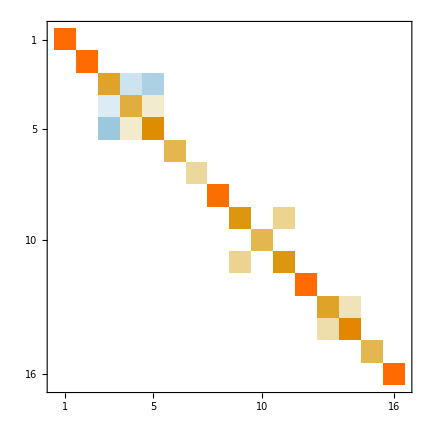

{16,16}

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | -1/(√2) | -1/(√6) | -1/(2 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | 0 | (√3)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 | -1/(2 √3) | 1/(√6) | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | √(2/3) | -1/(2 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/(√3) | 1/(√6) | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/2 | -1/(2 √3) | 1/(√6) | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | -1/(√2) | -1/(√6) | -1/(2 √3) | 0
0 | 1/2 | 1/(√2) | -1/(√6) | -1/(2 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/2 | -1/(2 √3) | 1/(√6) | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/(√3) | 1/(√6) | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | (√3)/2 | 0
0 | 0 | 0 | 0 | 0 | 1/2 | -1/(2 √3) | 1/(√6) | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | √(2/3) | -1/(2 √3) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/(√2) | -1/(√6) | -1/(2 √3) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

t4.mat

```mathematica
(*BLOCK DIAGONALISE N=4*)
(*generate vector space V for Sn*)

(*Example N=6*)
BlockPlot[4]
t4 = TransformMatrix[4] ;
t4// MatrixForm
Export["t4.mat", t4]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["t4.mat"]]]
```